# Read in second-order Ricci data

This notebook gives an example of reading in the output of the SecondOrderRicci code.
For more information see https://arxiv.org/abs/2006.11263.
The modes of second-order Ricci tensor (d2R) are outputted in the Barack-Lousto-Sago tensor spherical harmonic basis. See Appendix A of  https://arxiv.org/abs/1505.07841 for more details.

For ease of manipulating the data we use the SimulationTools package which can be downloaded from https://simulationtools.org/

```mathematica
<<SimulationTools`
```

```mathematica
M=1;
r0=11.1;
```

```mathematica
Ω= Sqrt[M/r0^3];
```

Change below to point to the directory with the source in it.

```mathematica
SetDirectory["~/Google Drive/My Drive/Second order data/Dense/d2R/r0_"<>ToString[r0]<>"/d2R_RetRet"];
```

```mathematica
rGrid=Import["Src.h5",{"Datasets","/r"}];
```

```mathematica
Loadd2R[i_,l_,m_]:=d2R[i,l,m]=ToDataTable@Transpose[{rGrid,Complex@@@Import["Src.h5",{"Datasets","/src i="<>ToString[i]<>" l="<>ToString[l]<>" m="<>ToString[m]}]}]
```

```mathematica
Do[Loadd2R[i,2,2],{i,1,7}]
```

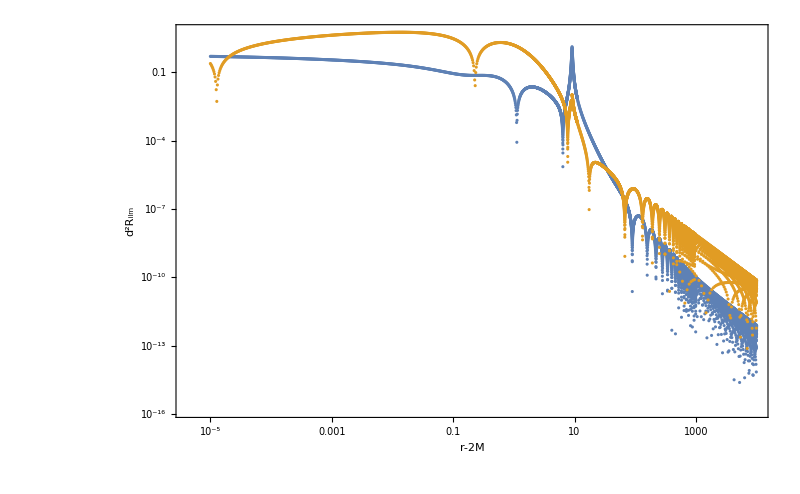

```mathematica
ListLogLogPlot[{Re[Shifted[d2R[1,2,2],-2]]//Abs,Re[Shifted[d2R[7,2,2],-2]]//Abs},PlotTheme->"Detailed",BaseStyle->20,FrameStyle->Black,FrameLabel->{"r-2M","d^2R_ilm"},ImageSize->800]
```

### Load the data on v or u slicing

```mathematica
rDT=ToDataTable[rGrid,rGrid];
```

Define the tortoise coordinates

```mathematica
rs[r_]:=r+2M Log[r/(2M)-1]
```

Change to v or u slicing by multiplying by the relevant exponential factor

```mathematica
d2RU[i_,l_,m_]:=d2R[i,l,m]Exp[-I m Ω rs[rDT]]
d2RV[i_,l_,m_]:=d2R[i,l,m]Exp[I m Ω rs[rDT]]
```

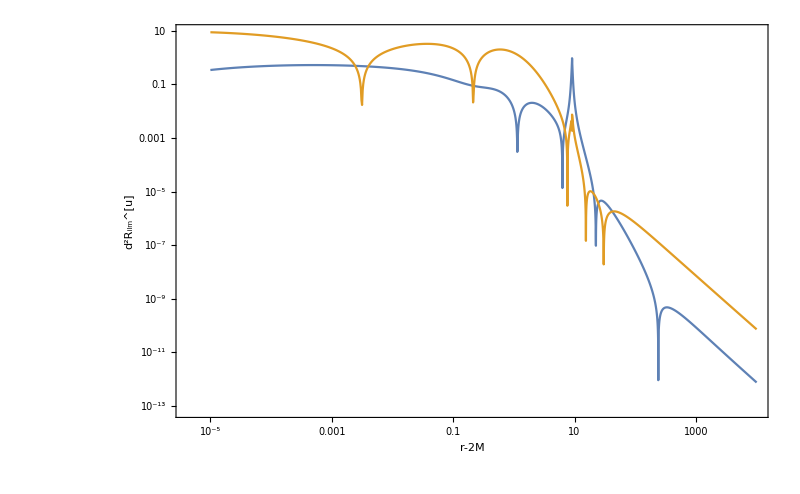

```mathematica
ListLogLogPlot[{Shifted[d2RU[1,2,2],-2]//Re//Abs,Shifted[d2RU[7,2,2],-2]//Re//Abs},PlotTheme->"Detailed",BaseStyle->20,FrameStyle->Black,FrameLabel->{"r-2M","d^2R_ilm^[u]"},ImageSize->800,Joined->True]
```